```mathematica
μB=1.39996;(*MHz/Gauss*)
```

## Zeeman Hamiltonian Matrix element calculator

```mathematica
(*calculator for Zeeman hamiltonian components for hunds case B only. Change J, Jprime, F and mf values to get matrix elements. Hzx is the sum of eqs 8.183 and 8.185 in B&C -> the spin and nuclear zeeman terms added together.Needs to be multiplied by μ_B. For Lambda =/= 0,+1*(-1)^(F-mf)ThreeJSymbol[{F,-mf},{1,0},{Fp,mf}](-1)^(Fp+J+1+S)Sqrt[(2Fp+1)(2F+1)]*SixJSymbol[{F,J,S},{Jp,Fp,1}](-1)^(Jp+n+1+S)Sqrt[(2Jp+1)(2J+1)]*SixJSymbol[{J,n,S},{np,Jp,1}]*(-1)^(n-Λ)ThreeJSymbol[{n,-Λ},{1,0},{np,Λ}]Sqrt[(2np+1)(2n+1)]*Λ*)
J=1/2;
Jp=1/2;
F=1;
Fp=1;
mf=1;
n=0;
np=0;
Λ=0;
Hzx=2*(-1)^(F-mf)ThreeJSymbol[{F,-mf},{1,0},{Fp,mf}](-1)^(Fp+J+1+S)Sqrt[(2Fp+1)(2F+1)]*SixJSymbol[{F,J,S},{Jp,Fp,1}](-1)^(J+n+1+S)Sqrt[(2Jp+1)(2J+1)]*SixJSymbol[{J,S,n},{S,Jp,1}]Sqrt[S(S+1)(2S+1)]+-(5.585/1836)*(-1)^(F-mf)ThreeJSymbol[{F,-mf},{1,0},{Fp,mf}](-1)^(F+J+1+S)Sqrt[(2Fp+1)(2F+1)]*SixJSymbol[{F,S,J},{S,Fp,1}]Sqrt[S(S+1)(2S+1)]
```

0.998479

## XSigma-ground state Full Hamiltonian

Heff is the effective hamiltonian, and Hz is the zeeman hamiltonian for the  N=1 ground state, with 2 spin split components.

```mathematica
Heff=({{2892.75, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 2892.75, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 2892.75, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 2892.75, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 2892.75, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 2861.4167, 0, 0, 22.156, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 2861.4167, 0, 0, 22.156, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 2861.4167, 0, 0, 22.156, 0}, {0, 0, 0, 0, 0, 22.156, 0, 0, -5765.92, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 22.156, 0, 0, -5765.92, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 22.156, 0, 0, -5765.92, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -5750.25}});
```

```mathematica
Hz=({{0.998479, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0.49924, 0, 0, 0, 0.289992, 0, 0, -0.815179, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0.334854, 0, 0, -0.941288, 0, 0}, {0, 0, 0, -0.49924, 0, 0, 0, 0.289992, 0, 0, -0.815179, 0}, {0, 0, 0, 0, -0.998479, 0, 0, 0, 0, 0, 0, 0}, {0, 0.289992, 0, 0, 0, 0.834094, 0, 0, 0.472165, 0, 0, 0}, {0, 0, 0.334854, 0, 0, 0, 0, 0, 0, 0, 0, -0.942809}, {0, 0, 0, 0.289992, 0, 0, 0, -0.834094, 0, 0, -0.472165, 0}, {0, -0.815179, 0, 0, 0, 0.472165, 0, 0, -0.334854, 0, 0, 0}, {0, 0, -0.941288, 0, 0, 0, 0, 0, 0, 0, 0, -0.331812}, {0, 0, 0, -0.815179, 0, 0, 0, -0.472165, 0, 0, 0.334854, 0}, {0, 0, 0, 0, 0, 0, -0.942809, 0, 0, -0.331812, 0, 0}});
Eigensystem[Heff+80*μB*Hz];
```

```mathematica
a[bz_]:=Eigenvalues[Heff+μB*bz*Hz][[5]];
b[bz_]:=Eigenvalues[Heff+μB*bz*Hz][[6]];
c[bz_]:=Eigenvalues[Heff+μB*bz*Hz][[7]];
d[bz_]:=Eigenvalues[Heff+μB*bz*Hz][[8]];
e[bz_]:=Eigenvalues[Heff+μB*bz*Hz][[9]];
f[bz_]:=Eigenvalues[Heff+μB*bz*Hz][[10]];
g[bz_]:=Eigenvalues[Heff+μB*bz*Hz][[11]];
h[bz_]:=Eigenvalues[Heff+μB*bz*Hz][[12]];
```

SetDelayed::write: Tag Integer in 299792458[bz_] is Protected.

```mathematica
avg32Mean[bz_]:=Mean[Eigenvalues[Heff+μB*bz*Hz][[5;;12]]];
```

```mathematica
2*(6491.98-5811.2)/1000
```

1.36156

```mathematica
Hnet=Heff+μB*(64.5)*Hz;
Hnet//MatrixForm
```

(2982.91 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2937.83 | 0 | 0 | 0 | 26.1855 | 0 | 0 | -73.6086 | 0 | 0 | 0
0 | 0 | 2892.75 | 0 | 0 | 0 | 30.2365 | 0 | 0 | -84.9959 | 0 | 0
0 | 0 | 0 | 2847.67 | 0 | 0 | 0 | 26.1855 | 0 | 0 | 73.6086 | 0
0 | 0 | 0 | 0 | 2802.59 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 26.1855 | 0 | 0 | 0 | 2936.73 | 0 | 0 | 64.7913 | 0 | 0 | -85.1332
0 | 0 | 30.2365 | 0 | 0 | 0 | 2861.42 | 0 | 0 | 22.156 | 0 | 0
0 | 0 | 0 | 26.1855 | 0 | 0 | 0 | 2786.1 | 0 | 0 | -20.4793 | 0
0 | -73.6086 | 0 | 0 | 0 | 64.7913 | 0 | 0 | -5796.16 | 0 | 0 | 0
0 | 0 | -84.9959 | 0 | 0 | 0 | 22.156 | 0 | 0 | -5765.92 | 0 | -29.9618
0 | 0 | 0 | 73.6086 | 0 | 0 | 0 | -20.4793 | 0 | 0 | -5735.68 | 0
0 | 0 | 0 | 0 | 0 | -85.1332 | 0 | 0 | 0 | -29.9618 | 0 | -5750.25)

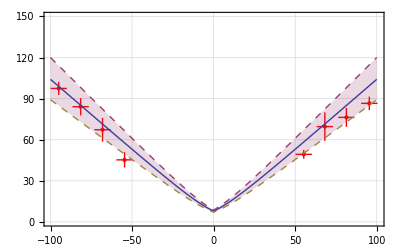

```mathematica
Needs["ErrorBarPlots`"]
EΠg=0.07*μB*0.5;(*Excited state EΠ g factor from polarization diff measurements*)
Xsigfields=13.568*{5.026,6,7.035,4.072,-5.02,-4.025,-6.01,-7};
XSigsplittings=2*Abs[{34.79,38.15,43.28,24.66,-33.65,-22.65,-42.05,-48.72}];
XSigsplittingsErrs={ErrorBar[5,10.4],ErrorBar[5,6.9],ErrorBar[5,4.9],ErrorBar[5,3.2],ErrorBar[5,8.7],ErrorBar[5,5.6],ErrorBar[5,6.3],ErrorBar[5,4.8]};
geoff=Show[ErrorListPlot[Transpose[{Transpose[{Xsigfields,XSigsplittings}],XSigsplittingsErrs}],PlotStyle->{PointSize[Large],Red}],Plot[{-(Eigenvalues[Heff+μB*bz*Hz][[1]]+Eigenvalues[Heff+μB*bz*Hz][[2]])/2+(Eigenvalues[Heff+μB*bz*Hz][[3]]+Eigenvalues[Heff+μB*bz*Hz][[4]])/2+2*(EΠg)*Abs[bz],(-(Eigenvalues[Heff+μB*bz*Hz][[1]]+Eigenvalues[Heff+μB*bz*Hz][[2]])/2+(Eigenvalues[Heff+μB*bz*Hz][[3]]+Eigenvalues[Heff+μB*bz*Hz][[4]])/2+2*(EΠg+0.025)*Abs[bz])*1.1,(-(Eigenvalues[Heff+μB*bz*Hz][[1]]+Eigenvalues[Heff+μB*bz*Hz][[2]])/2+(Eigenvalues[Heff+μB*bz*Hz][[3]]+Eigenvalues[Heff+μB*bz*Hz][[4]])/2+2*(EΠg-0.025)*Abs[bz])*0.9},{bz,-100,100},Filling->{2->{3}},PlotStyle->{Thick,Dashed,Dashed},PlotRange->{Automatic}],PlotRange->{0,150},Frame->True,LabelStyle->Directive[Medium],GridLines->Automatic]
```

```mathematica
Export["XsigZeemanPlots_3-8-17.png",geoff,ImageResolution->400]
```

XsigZeemanPlots_3-8-17.png

```mathematica
EΠg=-0.07*μB;(*Excited state EΠ g factor from polarization diff measurements*)
-EΠg*X32sigfields
```

```mathematica
Ecorr=1*{8.112502207600002,6.97740064,5.7849707104000005,-7.870645118000001,-4.946898656000001};
```

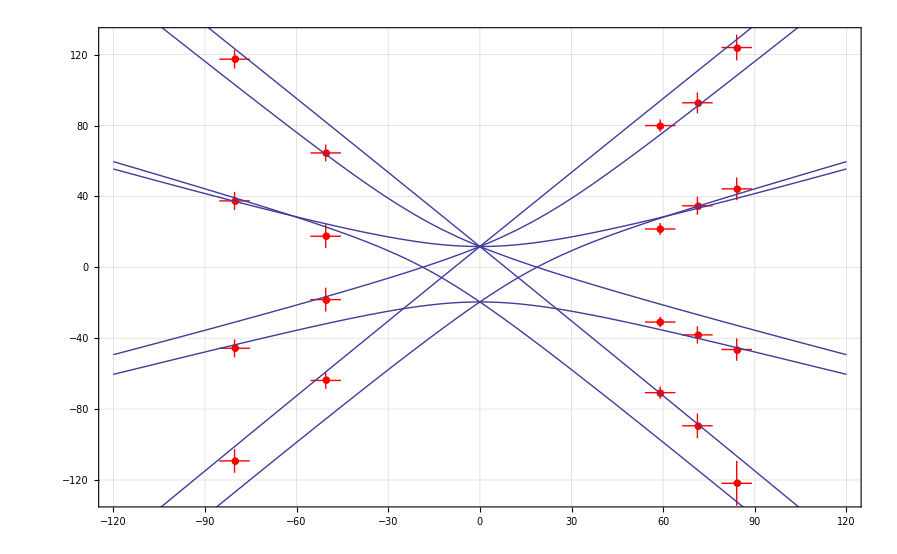

```mathematica
Needs["ErrorBarPlots`"]
X32sigfields=11.7*{7.1,6,4.96,-6.95,-4.4}+1;
X32Sigsplittings=-{{113.76473,82.4389,64.94478,-109.56427,-59.59404}+Ecorr,{38.27057,31.15825,25.0935,-29.60403,-12.5798}+Ecorr,{-36.15013,-27.74344,-15.84638,37.80402,13.27942}-Ecorr,{-115.88517,-85.85371,-74.1919,101.36428,58.89443}-Ecorr};
X32SigsplittingsErrs={{ErrorBar[5,12.61996],ErrorBar[5,6.91642],ErrorBar[5,3.45815],ErrorBar[5,5.32777],ErrorBar[5,4.74157]},{ErrorBar[5,6.32751],ErrorBar[5,4.87235],ErrorBar[5,2.94085],ErrorBar[5,5.11163],ErrorBar[5,6.73041]},{ErrorBar[5,6.39392],ErrorBar[5,5.10241],ErrorBar[5,3.31655],ErrorBar[5,5.06477],ErrorBar[5,6.73041]},{ErrorBar[5,7.21393],ErrorBar[5,5.87246],ErrorBar[5,3.43589],ErrorBar[5,6.65018],ErrorBar[5,4.74157]}};
x32data=Inner[List,X32sigfields,#,List]&/@X32Sigsplittings;
x32datae={};
For [i=1,i<5,i=i+1,
For[j=1,j<6,j=j+1,
x32datae=Append[x32datae,List[x32data[[i]][[j]],X32SigsplittingsErrs[[i]][[j]]]];
]
] 
X32plot=Show[ErrorListPlot[x32datae,PlotStyle->{Red},PlotMarkers->{●,10}],Plot[{Eigenvalues[Heff+μB*bz*Hz][[5;;12]]-avg32Mean[bz]},{bz,-120,120}],PlotRange->{-130,130},Frame->True,LabelStyle->Directive[Medium],GridLines->Automatic](*X32 data plus model, with center of mass subtracted out*)
```

```mathematica
Export["X32sigZeemanPlots_4-25-17.png",X32plot,ImageResolution->400]
```

X32sigZeemanPlots_4-25-17.png

Highfield Prediction:

```mathematica
(Mean[{2905.539592287832,2904.084595001446}]-Mean[{2921.2974841460923,2918.3879773648705}])/(-30)
```

0.484355

```mathematica
0.48435457036140783*(μB*0.5)
```

0.339039

```mathematica
1.397830660840009/(μB*1.5)
```

0.665653

```mathematica
2*Mean[{1.00152,0.998479}]/(μB*0.5)
```

2.85722

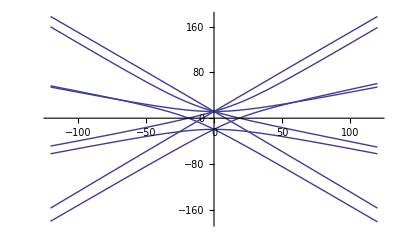

```mathematica
Plot[{Eigenvalues[Heff+μB*bz*Hz][[5;;12]]-avg32Mean[bz]},{bz,-120,120}]
```

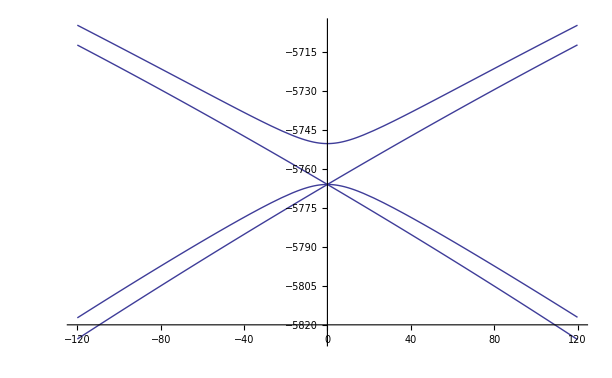

```mathematica
Plot[{Eigenvalues[Heff+μB*bz*Hz][[1;;4]]},{bz,-120,120}](*2nd curve from the top is mf=-1. its going up, so g-factor is negative. For the plot above, the very top curve is mf=+2, it goes up, so the g-factor is positive.*)
```

## BΣ state Zeeman Model:

Here, we only drive transitions from a single ground state peak, using orthogonal polarizations to find the splitting of the excited state. Therefore, we don't have to consider the ground state splitting.

```mathematica
BΣ=({{-0.01, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 50}});
HzBΣ=({{0.998479, 0, 0, 0}, {0, 0, 0, 1.00152}, {0, 0, -0.998479, 0}, {0, 1.00152, 0, 0}});
Eigensystem[BΣ+10*μB*HzBΣ]
```

{{53.6633,-13.9783,13.9683,-3.66331},{{0.,0.252789,0.,0.967521},{0.,0.,-1.,0.},{1.,0.,0.,0.},{0.,-0.967521,0.,0.252789}}}

```mathematica
(Mean[{-1537.61,-1517.49}]-Mean[{-139.78,-117.42}])/1000
```

-1.39895

```mathematica
avgBMean[bz_]:=Mean[Eigenvalues[BΣ+μB*bz*HzBΣ][[1;;4]]];
```

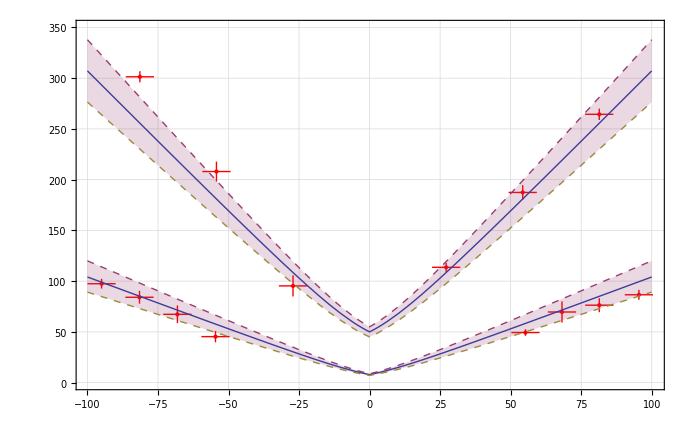

```mathematica
Bsigfields=13.568*{2,4,6,-6,-4,-2}-0;
BSigsplittings=2*Abs[{56.8,93.7,132.2,-150.69,-104,-47.65}];
BSigsplittingsErrs={ErrorBar[5,4.5],ErrorBar[5,7.2],ErrorBar[5,5.6],ErrorBar[5,5.5],ErrorBar[5,9.8],ErrorBar[5,10.4]};
BSigPlot=Show[ErrorListPlot[Transpose[{Transpose[{Bsigfields,BSigsplittings}],BSigsplittingsErrs}],PlotStyle->{PointSize[Large],Red}],Plot[{(Eigenvalues[BΣ+μB*bz*HzBΣ][[1]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[3]])/2-(Eigenvalues[BΣ+μB*bz*HzBΣ][[4]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[2]])/2+25,((Eigenvalues[BΣ+μB*bz*HzBΣ][[1]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[3]])/2-(Eigenvalues[BΣ+μB*bz*HzBΣ][[4]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[2]])/2+25)*1.1,((Eigenvalues[BΣ+μB*bz*HzBΣ][[1]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[3]])/2-(Eigenvalues[BΣ+μB*bz*HzBΣ][[4]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[2]])/2+25)*0.9},{bz,-100,100},Filling->{2->{3}},PlotStyle->{Thick,Dashed,Dashed},PlotRange->{0,350}],geoff,PlotRange->{0,350},Frame->True,LabelStyle->Directive[Medium],GridLines->Automatic]
```

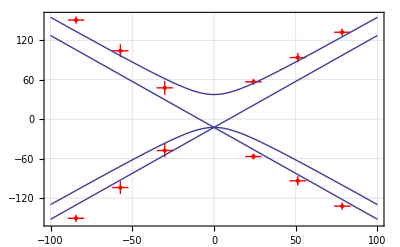

```mathematica
Bsigfields2=13.568*{2,4,6,-6,-4,-2,2,4,6,-6,-4,-2}-3;
BSigshifts={56.8,93.7,132.2,150.69,104,47.65,-56.8,-93.7,-132.2,-150.69,-104,-47.65};
BSigsplittingsErrs2={ErrorBar[5,4.5],ErrorBar[5,7.2],ErrorBar[5,5.6],ErrorBar[5,5.5],ErrorBar[5,9.8],ErrorBar[5,10.4],ErrorBar[5,4.5],ErrorBar[5,7.2],ErrorBar[5,5.6],ErrorBar[5,5.5],ErrorBar[5,9.8],ErrorBar[5,10.4]};
BSigPlot2=Show[ErrorListPlot[Transpose[{Transpose[{Bsigfields2,BSigshifts}],BSigsplittingsErrs2}],PlotStyle->{PointSize[Large],Red}],Plot[{Eigenvalues[BΣ+μB*bz*HzBΣ][[1;;4]]-avgBMean[bz]},{bz,-100,100},PlotRange->{-200,200}],Frame->True,LabelStyle->Directive[Medium],GridLines->Automatic](*Lowest curve is m=-1, it goes down, therefore, gfactor prediction is positive.*)
```

Highfield Prediction:

```mathematica
2*Mean[{1.00152,0.998479}]/(μB*0.5)
```

2.85722

```mathematica
Export["BsigZeemanPlots_3-8-17.png",Show[ErrorListPlot[Transpose[{Transpose[{Bsigfields,BSigsplittings}],BSigsplittingsErrs}],PlotStyle->{PointSize[Large],Red}],Plot[{(Eigenvalues[BΣ+μB*bz*HzBΣ][[1]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[3]])/2-(Eigenvalues[BΣ+μB*bz*HzBΣ][[4]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[2]])/2+25,((Eigenvalues[BΣ+μB*bz*HzBΣ][[1]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[3]])/2-(Eigenvalues[BΣ+μB*bz*HzBΣ][[4]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[2]])/2+25)*1.1,((Eigenvalues[BΣ+μB*bz*HzBΣ][[1]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[3]])/2-(Eigenvalues[BΣ+μB*bz*HzBΣ][[4]]+Eigenvalues[BΣ+μB*bz*HzBΣ][[2]])/2+25)*0.9},{bz,-100,100},Filling->{2->{3}},PlotStyle->{Thick,Dashed,Dashed},PlotRange->{Automatic}],Frame->True,LabelStyle->Directive[Medium],GridLines->Automatic],ImageResolution->400]
```

BsigZeemanPlots_3-8-17.png

## Data

```mathematica
BSshift=1.93;
APshift= 0.39;
XSshift=0.96;
X32shift=0.788;
EPshift=0.11;
{BSshift/(μB*0.5),0.04/(μB*0.5)}
{APshift/(μB*0.5),0.01/(μB*0.5)}
{XSshift/(μB*0.5),0.07/(μB*0.5)}
{EPshift/(μB*0.5),0.07/(μB*0.5)}
{X32shift/(μB),0.269/(μB)}
```

{2.75722,0.0571445}

{0.557159,0.0142861}

{1.37147,0.100003}

{0.157147,0.100003}

{0.562873,0.192148}

```mathematica
XS=(69.2986+86.82828)/4/(6*13.58)/0.5
XSerr=Sqrt[9.38764^2+6.53915^2]/4/(6*13.58)/0.5
```

0.958069

0.0702052

```mathematica
EP=(69.2986-86.82828)/4/(6*13.58)/0.5
EPerr=Sqrt[9.38764^2+6.53915^2]/4/(6*13.58)/0.5
```

-0.10757

0.0702052

```mathematica
BS ={1.91,1.94};
Mean[BS]
BSErr=Sqrt[0.06^2+0.06^2]/2
```

1.925

0.0424264

```mathematica
AP ={0.39,0.39};
Mean[AP]
APErr=Sqrt[0.02^2+0.02^2]/2
```

0.39

0.0141421

```mathematica
j32shifts={1.195/(3/2),0.389/(1/2),-0.384/(-1/2),-1.216/(-3/2)}
j32shiftsErr={.07/(3/2),.02/(1/2),.05/(1/2),.05/(3/2)};
Mean[j32shifts]
Sqrt[.07/(3/2)^2+.02/(1/2)^2+.04/(1/2)^2+.04/(3/2)^2]/2
```

{0.796667,0.778,0.768,0.810667}

0.788333

0.268742

```mathematica
.5*80*(0.5)*μB
```

27.9992

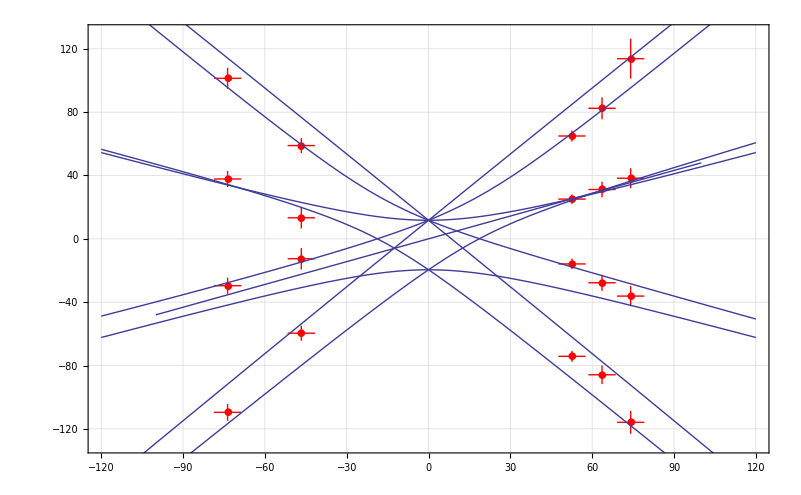

```mathematica
Show[X32plot,Plot[x*0.48,{x,-100,100}]]
```

```mathematica
(3/4+3/4-2)/(6/4)
```

-1/3